```mathematica
ClearAll[μ1,μ2,σ1,σ2,r,ϵ,x,r,z,h]

(*First Distribution: *)
f1[x_]:=(ⅇ^(-(x-μ1)^2/(2 σ1^2)))/(√(2 π) σ1);

(*Second Distribution: *)
f2[x_]:=(ⅇ^(-(x-μ2)^2/(2 σ2^2)))/(√(2 π) σ2);

(*Result of convolution: *)

conv[z_]=Convolve[f1[x],f2[-x],x,z]
```

```mathematica
conv[z_]=(ⅇ^(-(z-μ1+μ2)^2/(2 (σ1^2+σ2^2))))/(√(2 π)  √(σ1^2+σ2^2))
```

(ⅇ^(-(z-μ1+μ2)^2/(2 (σ1^2+σ2^2))))/(√(2 π) √(σ1^2+σ2^2))

```mathematica
(* Result of Integral from -ϵ to +ϵ : *)
```

```mathematica
integral[ϵ_]=Integrate[conv[z],{z,-ϵ,ϵ}]
```

```mathematica
(*So the Normalizing  Factor is: *)
1/2 (Erf[(ϵ+μ1-μ2)/(√2 √(σ1^2+σ2^2))]+Erf[(ϵ-μ1+μ2)/(√2 √(σ1^2+σ2^2))])
```

```mathematica
(*test values: *)
μ1=-40.0;
σ1=2.;
μ2=-41;
σ2=1.;
integral[1]
integral[2]
integral[3]
```

0.314453

0.582783

0.777634

```mathematica
ClearAll[μ1,μ2,σ1,σ2,r,ϵ,x,r,z,h,f]
```

```mathematica
(* After changing the integral order, The inner integral result from -ϵ to +ϵ :*)

f[h_]=Integrate[f1[h-x/2]*f2[h+x/2],{x,-ϵ,ϵ}]
```

```mathematica
f[h]=(ⅇ^(-(-2 h+μ1+μ2)^2/(2 (σ1^2+σ2^2))) (-Erf[((2 h-ϵ-2 μ2) σ1^2-(2 h+ϵ-2 μ1) σ2^2)/(2 √2 σ1 σ2 √(σ1^2+σ2^2))]+Erf[((2 h+ϵ-2 μ2) σ1^2+(-2 h+ϵ+2 μ1) σ2^2)/(2 √2 σ1 σ2 √(σ1^2+σ2^2))]))/(√(2 π) √(σ1^2+σ2^2))
```

```mathematica
(*Numerical test values: *)
μ1=-40.0;
σ1=2.;
μ2=-41;
σ2=1.;

ϵ=1;
NIntegrate[f[h],{h,-50,-30}]
ClearAll[ϵ];
ϵ=2;
NIntegrate[f[h],{h,-50,-30}]
ClearAll[ϵ];
ϵ=3;
NIntegrate[f[h],{h,-50,-30}]
ClearAll[ϵ];
```

0.314453

0.582783

0.777634

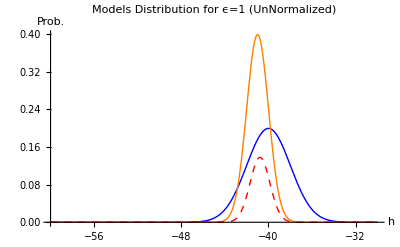

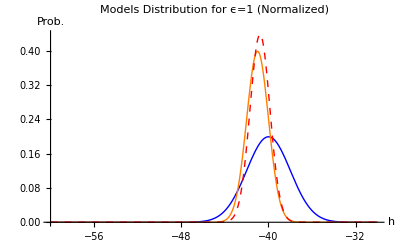

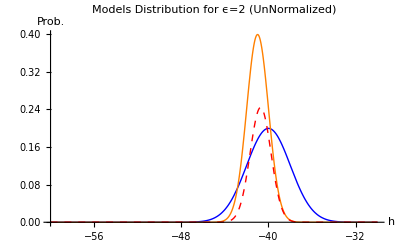

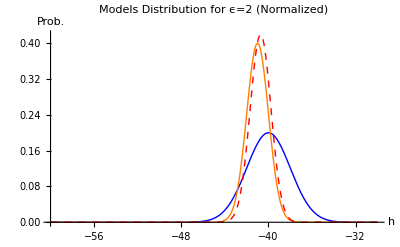

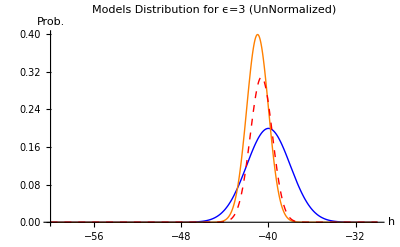

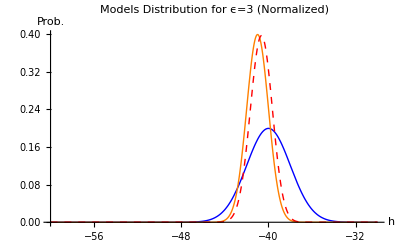

```mathematica
ϵ=1;
Plot[{f1[h],f2[h],f[h]},{h,-60,-30},PlotRange->Full,PlotStyle->{{Blue,Thick},{Orange,Thick},{Red,Thick,Dashed}},PlotLegend->{"M1(h)","M2(h)","M1 ∩ M2(h)"},LegendPosition->{1.1,-0.4},LegendShadow->None,PlotLabel->"Models Distribution for ϵ=1 (UnNormalized)",AxesLabel->{"h","Prob."}]
Plot[{f1[h],f2[h],f[h]/0.31445331523828146},{h,-60,-30},PlotRange->Full,PlotStyle->{{Blue,Thick},{Orange,Thick},{Red,Thick,Dashed}},PlotLegend->{"M1(h)","M2(h)","M1 ∩ M2(h)"},LegendPosition->{1.1,-0.4},LegendShadow->None,PlotLabel->"Models Distribution for ϵ=1 (Normalized)",AxesLabel->{"h","Prob."}]
ϵ=2;
Plot[{f1[h],f2[h],f[h]},{h,-60,-30},PlotRange->Full,PlotStyle->{{Blue,Thick},{Orange,Thick},{Red,Thick,Dashed}},PlotLegend->{"M1(h)","M2(h)","M1 ∩ M2(h)"},LegendPosition->{1.1,-0.4},LegendShadow->None,PlotLabel->"Models Distribution for ϵ=2 (UnNormalized)",AxesLabel->{"h","Prob."}]
Plot[{f1[h],f2[h],f[h]/0.5827833295503964},{h,-60,-30},PlotRange->Full,PlotStyle->{{Blue,Thick},{Orange,Thick},{Red,Thick,Dashed}},PlotLegend->{"M1(h)","M2(h)","M1 ∩ M2(h)"},LegendPosition->{1.1,-0.4},LegendShadow->None,PlotLabel->"Models Distribution for ϵ=2 (Normalized)",AxesLabel->{"h","Prob."}]
ϵ=3;
Plot[{f1[h],f2[h],f[h]},{h,-60,-30},PlotRange->Full,PlotStyle->{{Blue,Thick},{Orange,Thick},{Red,Thick,Dashed}},PlotLegend->{"M1(h)","M2(h)","M1 ∩ M2(h)"},LegendPosition->{1.1,-0.4},LegendShadow->None,PlotLabel->"Models Distribution for ϵ=3 (UnNormalized)",AxesLabel->{"h","Prob."}]
Plot[{f1[h],f2[h],f[h]/0.7776341801778637},{h,-60,-30},PlotRange->Full,PlotStyle->{{Blue,Thick},{Orange,Thick},{Red,Thick,Dashed}},PlotLegend->{"M1(h)","M2(h)","M1 ∩ M2(h)"},LegendPosition->{1.1,-0.4},LegendShadow->None,PlotLabel->"Models Distribution for ϵ=3 (Normalized)",AxesLabel->{"h","Prob."}]
```